{0.003122,0.003203,0.003174}

{0.003122,0.003122}

{0.003434,0.002812,0.002812}

{0.003434,0.002812}

{6.93589,16.4904,16.4945}

Ellipsoid[{0,0,0},{3.122,3.203,3.174}]

Ellipsoid[{0,0,0},{3.434,2.812,2.812}]

Ellipsoid[{0,0},{3.122,3.122}]

Ellipsoid[{0,0},{3.434,2.812}]

-Graphics3D-

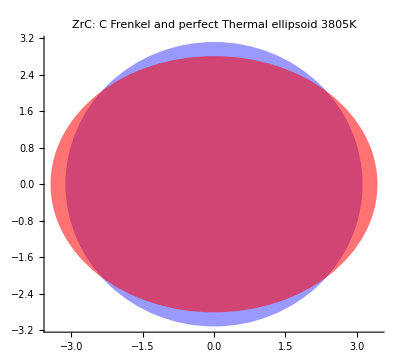

```mathematica
(*Mean thermal displacement at 3805K*)

meanthermalC={0.003122,0.003203,0.003174}
meanthermalC1={0.003122,0.003122}
meanthermalCdefect={0.003434,0.002812,0.002812}
meanthermalCdefect1={0.003434,0.002812}
{6.935892,16.490420,16.494476}
(*{Centre}, {major axes}*)

ellipse1=Ellipsoid[{0,0,0},meanthermalC*1000]
ellipse2=Ellipsoid[{0,0,0},meanthermalCdefect*1000]

ellipse3=Ellipsoid[{0,0},meanthermalC1*1000]
ellipse4=Ellipsoid[{0,0},meanthermalCdefect1*1000]

Graphics3D[{{Blue,Opacity[0.4],ellipse1},{Red,Opacity[0.55],ellipse2}},Boxed->False,Axes->True,AxesOrigin->{-3,-3,-3},PlotLabel->"ZrC: C Frenkel and perfect \n Thermal ellipsoid 3805K"]

Graphics[{{Blue,Opacity[0.4],ellipse3},{Red,Opacity[0.55],ellipse4}},Axes->True,AxesOrigin->{-3.5,-3.5},PlotLabel->"ZrC: C Frenkel and perfect \n Thermal ellipsoid 3805K"]
```



```mathematica
Graphics[Ellipsoid[{0,0},meanthermalC1]]
```

```mathematica
Table[Graphics3D[{Orange,Specularity[White,n],ellipse}],{n,{5,20,100}}]//TableForm;
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermal_displacement"];
files={"T_d_Zr_defect_allvols","T_d_C_defect_allvols","T_d_Zr_allvols","T_d_C_allvols"};
data=Table[ReadList[files[[i]],{Number, Number,Number, Number}],{i,1,4}];
(*first index file, last is volume*)
vol=Table[Partition[data[[1]],9][[j]],{j,1,9}];
vol[[1]]
```

{{0,0.001074,0.000857,0.000857},{500,0.005338,0.00365,0.00365},{1000,0.010544,0.007169,0.007169},{1500,0.015779,0.010716,0.010716},{2000,0.021021,0.014271,0.014271},{2500,0.026266,0.017829,0.017829},{3000,0.031513,0.021388,0.021388},{3500,0.036761,0.024948,0.024948},{4000,0.042009,0.028509,0.028509}}

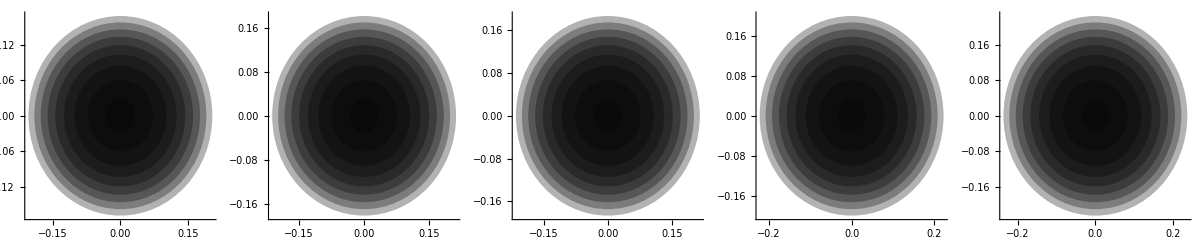

```mathematica
f[{T_,x_,y_,z_}]:=Ellipsoid[{0,0},{Sqrt[x],Sqrt[y]}]
GraphicsGrid[{Table[Graphics[{Opacity[0.3],Table[f[vol[[k]][[i]]],{i,1,9}]},Axes->True,AxesOrigin->{-0.25,-0.25}],{k,1,9,2}]},ImageSize->1200]
```

```mathematica
fEllipse[T_,x_,y_,z_]:=Evaluate@Ellipsoid[{0,0},{Sqrt[x],Sqrt[y]}]
testdata2=Table[fEllipse[testtdata[[i]]],{i,1,1}][[1]]
```

fEllipse[{0,0.001074,0.000857,0.000857}]

```mathematica
Graphics[Evaluate@{fEllipse[{0,0.001074,0.000857,0.000857}]}]
```

-Graphics-

```mathematica
Evaluate@testdata2[[1]]
```

fEllipse[{0,0.001074,0.000857,0.000857}]

```mathematica
testdata2[[1]]
```

fEllipse[{0,0.001074,0.000857,0.000857}]

```mathematica
Graphics[{Ellipsoid[{0,0},{√x,√y}]}]
```

-Graphics-

```mathematica
}
```